Author: Sam T Bush
Date: 9/9/2015

The purpose of this code is to read a fort.20 file generated for the east coast v6b_rivers grid, and output a table and graph of the flow timeseries at each river boundary as specified in that fort.20 file.

# Initialization Values

```mathematica
rivernodenums={{294228,294344,294457,294567 (*fishing ck*)},{295311,295299,295282,295259(*tar r*)},{281680,281959,282230,281940 (*contantnea ck*)},{293419,293541,293651,293758(*neuse r*)}};
gridfilepath="C:\\Users\\Sam\\Dropbox\\ADCIRC\\base grid\\fort.14";
slam0=-79.0;(*center longitude*)
sfea0=35.0;(*center latitude*)
filepath20="C:\\Users\\Sam\\Dropbox\\april2003\\cms20.txt";
```

# Calculate Constants

```mathematica
d2r=3.14159265358979323/180;
R=6378206.4;
slam0r=slam0*d2r;
sfea0r=sfea0*d2r;
```

# Import Fort.14 data

```mathematica
fort14=OpenRead[gridfilepath];
gridname=ToExpression[Read[fort14,Word]];
ne=ToExpression[Read[fort14,Number]];
nn=ToExpression[Read[fort14,Number]];

XYZ=Table[{NAN,NAN,NAN},{nn}];
Do[
Read[fort14,Number];
lon=Read[fort14,Number];
lat=Read[fort14,Number];
XYZ[[i,3]]=Read[fort14,Number];

slam=lon*d2r;
XYZ[[i,1]]=R*(slam-slam0r)*Cos[sfea0r];

sfea=lat*d2r;
XYZ[[i,2]]=R*sfea;
,{i,1,nn}];

Close[fort14];
halflengths=Table[{0,0},{Length[rivernodenums]}];


Do[
x1=XYZ[[rivernodenums[[i,1]],1]];
y1=XYZ[[rivernodenums[[i,1]],2]];

x2=XYZ[[rivernodenums[[i,2]],1]];
y2=XYZ[[rivernodenums[[i,2]],2]];

x3=XYZ[[rivernodenums[[i,3]],1]];
y3=XYZ[[rivernodenums[[i,3]],2]];

x4=XYZ[[rivernodenums[[i,4]],1]];
y4=XYZ[[rivernodenums[[i,4]],2]];

l1=((x1-x2)^2+(y1-y2)^2)^(1/2);
l2=((x2-x3)^2+(y2-y3)^2)^(1/2);
l3=((x3-x4)^2+(y1-y2)^2)^(1/2);

halflengths[[i,1]]=l1/2+l2/2;
halflengths[[i,2]]=l2/2+l3/2;

,{i,1,Length[rivernodenums]}];
```

```mathematica
halflengths
```

{{32.3746,37.3431},{41.1289,40.9843},{45.8878,47.1842},{63.279,63.2616}}

# Read fort.20

```mathematica
s20=OpenRead[filepath20];
timeinc=Read[s20,Number];
qs=ReadList[s20,Number];
Close[s20];

(*convert qs from a column into 8 columns, one for each node*)
qs=Partition[qs,24];
qs=Transpose[qs];
qs=Delete[qs,{{1},{2},{5},{6},{7},{8},{11},{12},{13},{14},{17},{18},{19},{20},{23},{24}}];

Qs=Table[qs[[i]]*Flatten[halflengths][[i]]+qs[[i+1]]*Flatten[halflengths][[i+1]],{i,1,8,2}];
```

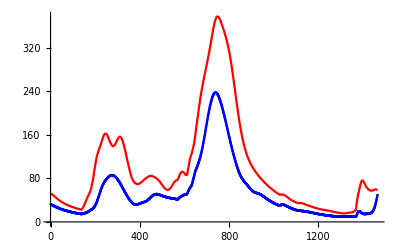

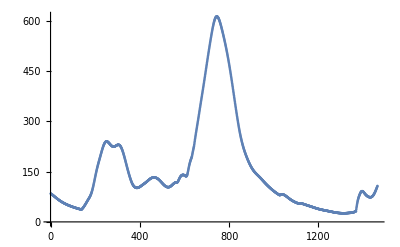

```mathematica
Show[ListPlot[Qs[[2]],PlotStyle->Red,PlotRange->All,Joined->True],ListPlot[Qs[[1]],PlotStyle->Blue]]

Show[ListPlot[Qs[[1]]+Qs[[2]],PlotRange->All]]
(*Check Qs[[1]], Joined - why does it truncate results?*)
```